```mathematica
SetDirectory@NotebookDirectory[];
Import["path to QuESTlink.m"];
CreateLocalQuESTEnv["path to quest_link"];
(*Read the paper [Tyson Jones and Simon Benjamin, arXiv:1912.07904] for how to setup the environment.*)
```

## Parameters

```mathematica
numQb=4;
PI=N[π,12];
```

## QC

```mathematica
ψIN=CreateQureg[numQb];
ψOUT=CreateQureg[numQb];
ψWP=CreateQureg[numQb];
```

## Basis

```mathematica
States=Table[{},{nN,1,2^(numQb/2)}];
Do[(
B=IntegerDigits[n-1,2,numQb];
circ=Table[If[B[[k+1]]==1,Subscript[X, k],Subscript[Z, k]],{k,0,numQb-1,1}];
ApplyCircuit[circ,ψIN,ψOUT];
OUT=Round[Abs[GetQuregMatrix[ψOUT]]];
index=Position[OUT,1][[1,1]];

BN=Table[B[[k+1]],{k,0,numQb-1,2}];
nN=FromDigits[BN,2]+1;
AppendTo[States[[nN]],index];
),{n,1,2^numQb}];
States;
```

```mathematica
ProNeurons[OUT_]:=(
Pro=Table[
P=0;
Do[P=P+OUT[[States[[i,j]]]],{j,1,2^(numQb/2)}];
P
,{i,1,2^(numQb/2)}];
Return[Pro]
)
```

## Neural Network Cirucit

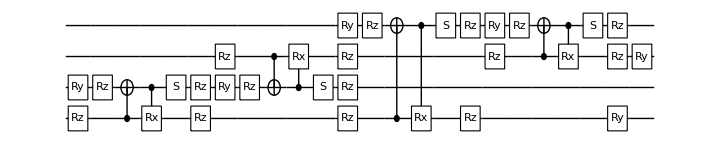

```mathematica
circuitNN[θlist_]:=(
circNN={};
Do[(
j=(b+1)/2;
Do[(
i=(a+2)/2;
ϕ=θlist[[numQb(j-1)+2i-1]];
θ=θlist[[numQb(j-1)+2i]];
circMR={Subscript[Rz, a][θ],Subscript[Rz, b][θ],Subscript[C, a][Subscript[X, b]],Subscript[C, b][Subscript[Rx, a][PI-2θ]],Subscript[S, b],Subscript[Rz, b][-θ],Subscript[Rz, a][-θ]};
circNN=Join[circNN,{Subscript[Ry, b][ϕ]},circMR];
),{a,0,numQb-1,2}]
),{b,1,numQb-1,2}];
Do[(
i=(a+2)/2;
ϕ=θlist[[numQb^2/2+i]];
circNN=Join[circNN,{Subscript[Ry, a][ϕ]}];
),{a,0,numQb-1,2}];
Return[circNN]
)
circNN=circuitNN[{0.0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9}];
DrawCircuit@circNN
```

## Distance

```mathematica
circNeurons=Table[Subscript[H, i],{i,0,numQb-1,2}];
DrawCircuit@circNeurons
circBell={{Subscript[H, 1],Subscript[C, 1][Subscript[X, 3]]},{Subscript[H, 1],Subscript[Z, 1],Subscript[C, 1][Subscript[X, 3]]},{Subscript[H, 1],Subscript[C, 1][Subscript[X, 3]],Subscript[X, 3]},{Subscript[H, 1],Subscript[Z, 1],Subscript[C, 1][Subscript[X, 3]],Subscript[X, 3]}};
DrawCircuit@circBell[[1]]
DrawCircuit@circBell[[2]]
DrawCircuit@circBell[[3]]
DrawCircuit@circBell[[4]]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
Clear[Distance]
Distance[θlist_/;(And@@(NumericQ/@θlist))]:=(
circNN=circuitNN[θlist];

ProN={};
Do[(
circ=Join[circNeurons,circBell[[i]],circNN];
ApplyCircuit[circ,ψIN,ψOUT];
OUT=Abs[GetQuregMatrix[ψOUT]]^2;
AppendTo[ProN,ProNeurons[OUT]];
),{i,1,4}];

Dis=0;
Do[(
Do[(
Dis=Dis+Total[Abs[ProN[[i]]-ProN[[j]]]]/12;
),{j,i+1,4}];
),{i,1,3}];

Return[Dis]
)
Distance[{0,0,0,0,0,0,0,0,-PI/2,0}]
ProN
```

1.

{{1.,3.7494×10^-33,3.08149×10^-33,3.79823×10^-65},{3.08149×10^-33,3.79823×10^-65,1.,3.7494×10^-33},{7.4988×10^-33,1.,7.59645×10^-65,3.08149×10^-33},{7.59645×10^-65,3.08149×10^-33,7.4988×10^-33,1.}}

## Find

{1.,{0_1→-1.01995×10^-9,0_2→-1.73836×10^-8,0_3→-0.319734,0_4→-1.30648,0_5→-6.75629×10^-10,0_6→3.23498×10^-8,0_7→2.35314×10^-9,0_8→-8.01567×10^-11,0_9→-1.5708,0_10→-1.86259×10^-8}}

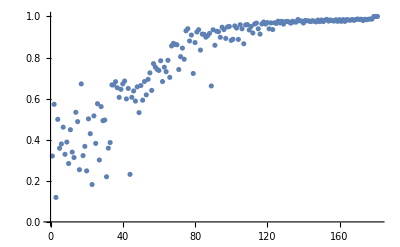

```mathematica
θlist=Table[Subscript[θ, i],{i,1,(numQb+1)numQb/2}];
{res,data}=Reap[NMaximize[Distance[θlist],θlist,EvaluationMonitor:>Sow[Distance[θlist]]]];
res
plot=ListPlot[data]
```

## Optimal Parameters

```mathematica
θlist/.Last[res]
Distance[{0.0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9}]
ProN
Distance[θlist/.Last[res]]
ProN
```

{-1.01995×10^-9,-1.73836×10^-8,-0.319734,-1.30648,-6.75629×10^-10,3.23498×10^-8,2.35314×10^-9,-8.01567×10^-11,-1.5708,-1.86259×10^-8}

0.459396

{{0.131181,0.0897623,0.276689,0.502368},{0.216691,0.581412,0.107137,0.0947597},{0.160736,0.0413739,0.446198,0.351692},{0.446956,0.331888,0.115524,0.105632}}

1.

{{1.,3.77816×10^-16,3.51643×10^-16,2.96387×10^-20},{3.51643×10^-16,7.18745×10^-19,1.,3.77816×10^-16},{8.663×10^-17,1.,7.18745×10^-19,3.51643×10^-16},{2.96387×10^-20,3.51643×10^-16,8.663×10^-17,1.}}

## Data and Plot

```mathematica
file=File["Bell_find.dat"];
toFile={};
AppendTo[toFile,"Optimal distance:"];
AppendTo[toFile,res[[1]]];
AppendTo[toFile,""];
AppendTo[toFile,"Optimal parameters:"];
AppendTo[toFile,θlist/.Last[res]];
AppendTo[toFile,""];
AppendTo[toFile,"Evaluations:"];
AppendTo[toFile,data];
AppendTo[toFile,""];
Export[file,toFile];
```

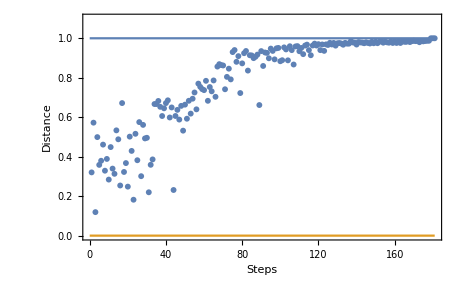

```mathematica
plot=ListPlot[Transpose[{Range[1,Length[data[[1]]]],data[[1]]}],PlotRange->{{0,Length[data[[1]]]},{0,1.1}},Axes->{False,False},Frame->True,FrameLabel->{"Steps","Distance"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->{460,Automatic},LabelStyle->{FontSize->18}];
plotQC=ListLinePlot[{{{0,1},{Length[data[[1]]],1}},{{0,0},{Length[data[[1]]],0}}}];
Show[plot,plotQC]
```